```mathematica
Timing[
$HistoryLength=3;
ClearAll[Lz,XY,XZ,YZ];

clight=2.99792458*10^8;(*Speed of light*)

(*List of initial particle radius and energy*)

Rad[1]={"4e-3","8e-3","1.6e-2","2.4e-2","3.2e-2","4e-2","4.8e-2","5.6e-2","6.4e-2","7.2e-2"};
Eneg[1]={"4.823e5","1.928e6","1.198e7","4.705e7","1.763e8","3.633e8","5.870e8","8.333e8","1.094e9","1.365e9","1.641e9","1.923e9","2.208e9"};

(* Read in data file: put your directory path here *)

Table[orb[i,j]=Import["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/solenoid_scipy/result/pthe_0_sl30cm/alldata_amp"<>ToString[Rad[1][[j]]]<>"_velo0_kene"<>ToString[Eneg[1][[i]]]<>"_sleng30cm_step6001.dat","Table"],{i,1,13},{j,1,10}];

LENG[1]=Length[orb[1,1]];
Table[X[i,j]=orb[i,j][[All,1]],{i,1,13},{j,1,10}];
Table[Vx[i,j]=orb[i,j][[All,2]],{i,1,13},{j,1,10}];
Table[Y[i,j]=orb[i,j][[All,3]],{i,1,13},{j,1,10}];
Table[Vy[i,j]=orb[i,j][[All,4]],{i,1,13},{j,1,10}];
Table[Z[i,j]=orb[i,j][[All,5]],{i,1,13},{j,1,10}];
Table[Vz[i,j]=orb[i,j][[All,6]],{i,1,13},{j,1,10}];
Table[Xy[i,j]=orb[i,j][[All,{1,3}]],{i,1,13},{j,1,10}];
Table[RZ[i,j]=Table[{Z[i,j][[n]],(X[i,j][[n]]^2+Y[i,j][[n]]^2)^0.5},{n,1,LENG[1]}],{i,1,13},{j,1,10}];
Table[PT[i,j]=orb[i,j][[All,{5,7}]],{i,1,13},{j,1,10}];


Table[Beta3d[i,j]=Table[{Z[i,j][[n]],√(Vx[i,j][[n]]^2+Vy[i,j][[n]]^2+Vz[i,j][[n]]^2)/clight},{n,1,LENG[1]}],{i,1,13},{j,1,10}];
Table[Betaz[i,j]=Table[{Z[i,j][[n]],√(Vz[i,j][[n]]^2)/clight},{n,1,LENG[1]}],{i,1,13},{j,1,10}];
Table[Gamma3d[i,j]=Table[{Z[i,j][[n]],√(1/(1-((Vx[i,j][[n]]^2+Vy[i,j][[n]]^2+Vz[i,j][[n]]^2)/clight^2)))},{n,1,LENG[1]}],{i,1,13},{j,1,10}];
Table[Gammaz[i,j]=Table[{Z[i,j][[n]],√(1/(1-((Vz[i,j][[n]]^2)/clight^2)))},{n,1,LENG[1]}],{i,1,13},{j,1,10}];

]
```

{156.52309,Null}

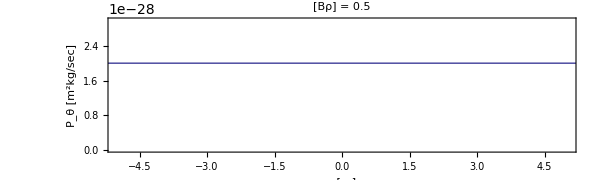

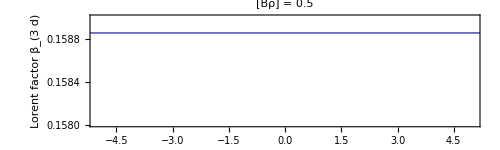

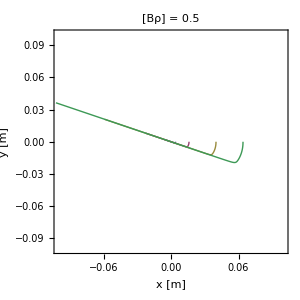

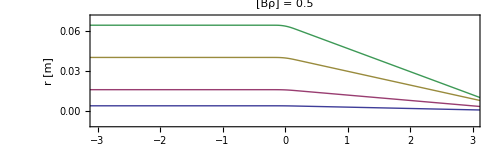

```mathematica
(*Sample plot for basic confirmation*)

Pthe[1]=ListPlot[Table[PT[3,i],{i,{7}}],PlotRange->{{-5,5},{0,3*10^-28}},Axes->None,AspectRatio->0.3,Joined->True,Frame->True,FrameLabel->{"z [m]","P_θ [m^2kg/sec]"},LabelStyle->Directive[11],ImageSize->{600,180},PlotLabel->Style["[Bρ] = 0.5",15]]

B3d[1]=ListPlot[Table[Beta3d[3,i],{i,{7}}],PlotRange->{{-5,5},{0.158,0.159}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","Lorent factor β_(3  d)"},LabelStyle->Directive[15],PlotLabel->Style["[Bρ] = 0.5",15],PlotStyle->ColorData[1,"ColorList"]]

XY[1]=ListPlot[Table[Xy[3,i],{i,{1,3,6,9}}],PlotRange->{{-0.1,0.1},{-0.1,0.1}},AspectRatio->1,ImageSize->{300,300},Axes->None,Joined->True,Frame->True,FrameLabel->{"x [m]","y [m]"},LabelStyle->Directive[18],PlotLabel->Style["[Bρ] = 0.5",18],PlotStyle->ColorData[1,"ColorList"]]

Rz[1]=ListPlot[Table[RZ[3,i],{i,{1,3,6,9}}],PlotRange->{{-3,3},{-0.01,0.07}},AspectRatio->0.3,ImageSize->{500,180},Axes->None,Joined->True,Frame->True,FrameLabel->{"z [m]","r [m]"},LabelStyle->Directive[14],PlotLabel->Style["[Bρ] = 0.5",15],PlotStyle->ColorData[1,"ColorList"]]
```

```mathematica
(*Export graphic data to the directory on your computer:you have to specify the directory where you want to export*)

Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0_basic1/Ptheta_sample.eps",Pthe[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0_basic1/Beta_sample.eps",B3d[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0_basic1/XY_sample.eps",XY[1],"EPS"];
Export["/Users/oosakikazuya/Documents/warp_wk1/warp/solenoid/graphics/scipy_nonlinear/Ptheta0_basic1/RZ_sample.eps",Rz[1],"EPS"];
```